```mathematica
Needs["CCompilerDriver`"]

randomRealOwenLib=CreateLibrary[{"G:\\git\\Miscellaneous\\MathematicaNotebooks\\Samplers\\C++\\LibraryLink\\randomRealOwen.cpp"},"randomRealOwen","Debug"->False, "CompileOptions"->"-O3"]

RandomRealOwen=LibraryFunctionLoad[randomRealOwenLib,"RandomRealOwen",{Integer},Real]
RandomRealOwen2D=LibraryFunctionLoad[randomRealOwenLib,"RandomRealOwen2D",{Integer},{Real,1}]

RandomRealOwen[123]
RandomRealOwen2D[123]
```

C:\Users\max\AppData\Roaming\Mathematica\SystemFiles\LibraryResources\Windows-x86-64\randomRealOwen.dll

LibraryFunction[…]

LibraryFunction[…]

0.179594

{0.179594,0.231584}

```mathematica
Needs["CCompilerDriver`"]
randomRealHaltonLib=CreateLibrary[{"G:\\git\\Miscellaneous\\MathematicaNotebooks\\Samplers\\C++\\LibraryLink\\randomRealHalton.cpp"},"randomRealHalton","Debug"->False, "CompileOptions"->"-O3"]
RandomRealHalton=LibraryFunctionLoad[randomRealHaltonLib,"RandomRealHalton",{Integer},Real]
RandomRealHalton2D=LibraryFunctionLoad[randomRealHaltonLib,"RandomRealHalton2D",{Integer},{Real,1}]

RandomRealHalton[123688]
RandomRealHalton2D[123688]
```

C:\Users\max\AppData\Roaming\Mathematica\SystemFiles\LibraryResources\Windows-x86-64\randomRealHalton.dll

LibraryFunction[…]

LibraryFunction[…]

0.319355

{0.0811691,0.33685}

```mathematica
Needs["CCompilerDriver`"]
randomRealCMJLib=CreateLibrary[{"G:\\git\\Miscellaneous\\MathematicaNotebooks\\Samplers\\C++\\LibraryLink\\randomRealCMJ.cpp"},"randomRealCMJ","Debug"->False, "CompileOptions"->"-O3"]
RandomRealCMJ=LibraryFunctionLoad[randomRealCMJLib,"RandomRealCMJ",{Integer},Real]
RandomRealCMJ2D=LibraryFunctionLoad[randomRealCMJLib,"RandomRealCMJ2D",{Integer,Integer},{Real,1}]

RandomRealCMJ[15]
RandomRealCMJ2D[15,24]
```

C:\Users\max\AppData\Roaming\Mathematica\SystemFiles\LibraryResources\Windows-x86-64\randomRealCMJ.dll

LibraryFunction[…]

LibraryFunction[…]

0.314911

{0.579999,0.752401}

```mathematica
Needs["CCompilerDriver`"]
randomRealR2Lib=CreateLibrary[{"G:\\git\\Miscellaneous\\MathematicaNotebooks\\Samplers\\C++\\LibraryLink\\randomRealR2.cpp"},"randomRealR2","Debug"->False, "CompileOptions"->"-O3"]
RandomRealR2=LibraryFunctionLoad[randomRealR2Lib,"RandomRealR2",{Integer},Real]
RandomRealR22D=LibraryFunctionLoad[randomRealR2Lib,"RandomRealR22D",{Integer},{Real,1}]

RandomRealR2[123]
RandomRealR22D[123]
```

C:\Users\max\AppData\Roaming\Mathematica\SystemFiles\LibraryResources\Windows-x86-64\randomRealR2.dll

LibraryFunction[…]

LibraryFunction[…]

0.856659

{0.856659,0.0903625}

```mathematica
Needs["CCompilerDriver`"]
randomRealLDBNLib=CreateLibrary[{"G:\\git\\Miscellaneous\\MathematicaNotebooks\\Samplers\\C++\\LibraryLink\\randomRealLDBN.cpp"},"randomRealLDBN","Debug"->False, "CompileOptions"->"-O3"]

RandomRealLDBN=LibraryFunctionLoad[randomRealLDBNLib,"RandomRealLDBN",{Integer},{Real,2}]
RandomRealLDBN[4]
```

C:\Users\max\AppData\Roaming\Mathematica\SystemFiles\LibraryResources\Windows-x86-64\randomRealLDBN.dll

LibraryFunction[…]

{{0.25,0.4375},{0.6875,0.125},{0.40625,0.9375},{0.8125,0.625}}

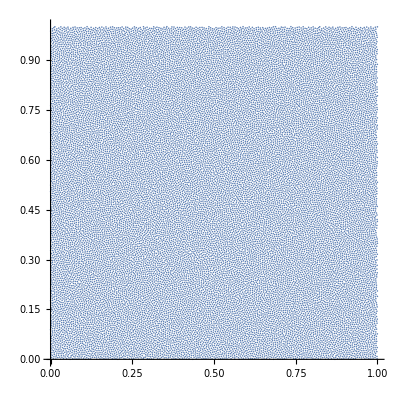

```mathematica
Clear[data];
data=RandomRealLDBN[25000];
ListPlot[data,ImageSize->Full,AspectRatio->1]
```